# Equivalence k-n

## Chercher un effet équivalent de l’aggrégation des risques temporel (maturation time variability) et spatial (pseudointerférence du parasitisme) Modèle de référence : Murdoch 1987 (DDE)

```mathematica
Clear[Global`*]
```

## Murdoch 1987 (DDE) : effet de l’ajout de pseudointerférence

## Système

On définit B[t] = ∫_(t-τ1)^t (k Log[1+a P2[u]/k]+ δH1)ⅆu
Alors on peut dériver B[t] :

```mathematica
D[∫_(t-τ1)^t (k Log[1+a P2[u]/k] + δH1)ⅆu, t]
```

k Log[1+(a P2[t])/k]-k Log[1+(a P2[t-τ1])/k]

Et on l’intègre dans le système d’ED sous forme dérivée

```mathematica
X[t_]:= k Log[1+a P2[t]/k];
R[t_] := ρ δH2 H2[t];
MH[t] = R[t-τ1] Exp[-B[t]];
Par[t_] := X[t]*H1[t];
MP[t] = Par[t-τ2] Exp[-δP1 τ2];

systemePI = {
H1'[t] ==   R[t]-MH[t] - Par[t] - δH1 H1[t],
H2'[t] == MH[t] - δH2 H2[t],
P1'[t] == Par[t] - MP[t] - δP1 P1[t],
P2'[t] == MP[t] - δP2 P2[t],
B'[t] == X[t] - X[t-τ1]
}

parPI = {τ1->1, δH1->0 ,δP1->1, a->1, δP2 -> 8, ρ->33, k->0.5}
```

{H1'[t]==-δH1 H1[t]+δH2 ρ H2[t]-ⅇ^(-B[t]) δH2 ρ H2[t-τ1]-k H1[t] Log[1+(a P2[t])/k],H2'[t]==-δH2 H2[t]+ⅇ^(-B[t]) δH2 ρ H2[t-τ1],P1'[t]==k H1[t] Log[1+(a P2[t])/k]-ⅇ^(-δP1 τ2) k H1[t-τ2] Log[1+(a P2[t-τ2])/k]-δP1 P1[t],P2'[t]==ⅇ^(-δP1 τ2) k H1[t-τ2] Log[1+(a P2[t-τ2])/k]-δP2 P2[t],B'[t]==k Log[1+(a P2[t])/k]-k Log[1+(a P2[t-τ1])/k]}

{τ1→1,δH1→0,δP1→1,a→1,δP2→8,ρ→33,k→0.5}

## Simulations numériques

Que vaut B[0] ?

```mathematica
P20temp = 10;
B0 =  τ1(k Log[1+a P20temp/k]+ δH1)/.parsimu // N
```

ReplaceAll::reps: {parsimu} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

τ1 (δH1+k Log[1.+(10. a)/k])/.parsimu

```mathematica
parsimu = {τ1->1, δH1->0 ,δP1->1, a->1, δP2 -> 8, ρ->33, k->1,τ2->1, δH2 -> 1/0.01}
leqnIC = Flatten[{systemePI, {H1[t/;t<=0] ==10, H2[t/;t<=0] ==10, P1[t/;t<=0] ==10, P2[t/;t<=0] ==10, B[t/;t<=0] ==τ1(k Log[1+a P20temp/k]+ δH1)/.parsimu // N}}];
sol=NDSolve[leqnIC/.parsimu, {H1, H2, P1, P2,B},{t, 0,500}];
```

{τ1→1,δH1→0,δP1→1,a→1,δP2→8,ρ→33,k→1,τ2→1,δH2→100.}

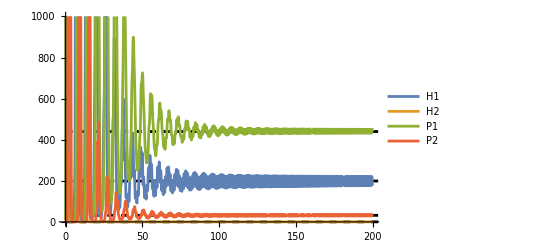

```mathematica
positions={H1eq,H2eq,P1eq,P2eq} /.parsimu;
minMax={0,500};
Show[Plot[Evaluate[{H1[t],H2[t], P1[t],P2[t]}/. sol[[1]]],{t,0,200},
PlotLegends->{"H1", "H2", "P1", "P2"},
PlotRange->{{0,200},{0,1000}}],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{minMax[[1]],x},{minMax[[2]],x}}],{x,positions}]}
]
```

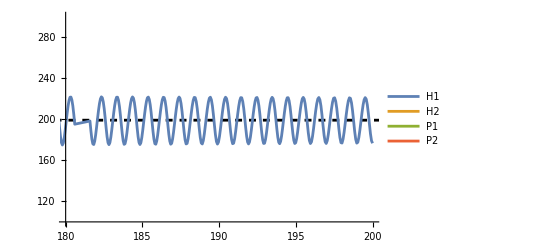

```mathematica
positions={H1eq,H2eq,P1eq,P2eq} /.parsimu;
minMax={0,500};
Show[Plot[Evaluate[{H1[t],H2[t], P1[t],P2[t]}/. sol[[1]]],{t,0,200},
PlotLegends->{"H1", "H2", "P1", "P2"},
PlotRange->{{180,200},{100,300}}],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{minMax[[1]],x},{minMax[[2]],x}}],{x,positions}]}
]
```

## Equilibre non trivial

```mathematica
Clear[P2eq];
Xeq = k Log[1+a P2eq/k];
α = Exp[-τ2 δP1];

H1eq = P2eq * δP2/(Xeq α) // FullSimplify
H2eq = H1eq * (Xeq + δH1)/(δH2(ρ-1)) // FullSimplify
P1eq = H1eq * (Xeq(1-α))/δP1 // FullSimplify
P2eq = k/a(Exp[1/k(Log[ρ]/τ1-δH1)]-1) // FullSimplify
Beq = -τ1(Xeq+δH1) // FullSimplify
```

(ⅇ^(δP1 τ2) P2eq δP2)/(k Log[1+(a P2eq)/k])

(ⅇ^(δP1 τ2) P2eq δP2 (δH1+k Log[1+(a P2eq)/k]))/(k δH2 (-1+ρ) Log[1+(a P2eq)/k])

((-1+ⅇ^(δP1 τ2)) P2eq δP2)/δP1

((-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k)/a

-τ1 (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])

```mathematica
H2eq // FullSimplify
```

(ⅇ^(δP1 τ2) (-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) δP2 (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))/(a δH2 (-1+ρ) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])

### Equilibres quand k -> + ∞ : on devrait retrouver les équilibres du Murdoch 1987

```mathematica
Limit[{H1eq, H2eq, P1eq, P2eq}, k-> + ∞]// FullSimplify
```

{(ⅇ^(δP1 τ2) δP2)/a,-(ⅇ^(δP1 τ2) δP2 Log[ρ])/(a δH2 τ1-a δH2 ρ τ1),-((-1+ⅇ^(δP1 τ2)) δP2 (δH1 τ1-Log[ρ]))/(a δP1 τ1),(-δH1 τ1+Log[ρ])/(a τ1)}

On a bien les équilibres du Murdoch 1987 (cf juste au dessus)

## Linéarisation

```mathematica
Clear[H1eq, H2eq, P1eq, P2eq, ϕeq, ψeq, Xeq, α];
systemePILin = {
nH1'[t] ==   nR[t]-nMH[t] - nPar[t] - δH1 nH1[t],
nH2'[t] == nMH[t] - δH2 nH2[t],
nP1'[t] == nPar[t] - nMP[t] - δP1 nP1[t],
nP2'[t] == nMP[t] - δP2 nP2[t]
};

nR[t] = ρ δH2 nH2[t];
nMH[t] = ρ δH2 Exp[-ϕeq] (nH2[t-τ1] - H2eq ψeq ∫_(t-τ1)^t nP2[u]ⅆu);
nPar[t_] := Xeq nH1[t] + ψeq H1eq nP2[t]; (* Non evaluated function to deal witg t-τ2 after *)
nMP[t] = α nPar[t-τ2];

systemePILin
```

{nH1'[t]==-Xeq nH1[t]-δH1 nH1[t]+δH2 ρ nH2[t]-ⅇ^-ϕeq δH2 ρ (-H2eq ψeq ∫_(t-τ1)^t nP2[u]ⅆu+nH2[t-τ1])-H1eq ψeq nP2[t],nH2'[t]==-δH2 nH2[t]+ⅇ^-ϕeq δH2 ρ (-H2eq ψeq ∫_(t-τ1)^t nP2[u]ⅆu+nH2[t-τ1]),nP1'[t]==Xeq nH1[t]-δP1 nP1[t]+H1eq ψeq nP2[t]-α (Xeq nH1[t-τ2]+H1eq ψeq nP2[t-τ2]),nP2'[t]==-δP2 nP2[t]+α (Xeq nH1[t-τ2]+H1eq ψeq nP2[t-τ2])}

```mathematica
Xeq = k Log[1+a P2eq/k];
α = Exp[-τ2 δP1];
ϕeq = τ1(δH1 + k Log[1+a P2eq/k]);
ψeq = (a k)/(k+a P2eq);
H1eq = P2eq * δP2/(Xeq α) // FullSimplify;
H2eq = H1eq * (Xeq + δH1)/(δH2(ρ-1)) // FullSimplify;
P1eq = H1eq * (Xeq(1-α))/δP1 // FullSimplify;
P2eq = k/a(Exp[1/k(Log[ρ]/τ1-δH1)]-1) // FullSimplify;
systemePILin
```

{nH1'[t]==-δH1 nH1[t]-k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))] nH1[t]+δH2 ρ nH2[t]-ⅇ^(-τ1 (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])) δH2 ρ (-(ⅇ^(δP1 τ2) (-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k δP2 (∫_(t-τ1)^t nP2[u]ⅆu) (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))/((k+(-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k) δH2 (-1+ρ) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])+nH2[t-τ1])-(ⅇ^(δP1 τ2) (-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k δP2 nP2[t])/((k+(-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]),nH2'[t]==-δH2 nH2[t]+ⅇ^(-τ1 (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])) δH2 ρ (-(ⅇ^(δP1 τ2) (-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k δP2 (∫_(t-τ1)^t nP2[u]ⅆu) (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))/((k+(-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k) δH2 (-1+ρ) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])+nH2[t-τ1]),nP1'[t]==k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))] nH1[t]-δP1 nP1[t]+(ⅇ^(δP1 τ2) (-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k δP2 nP2[t])/((k+(-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])-ⅇ^(-δP1 τ2) (k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))] nH1[t-τ2]+(ⅇ^(δP1 τ2) (-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k δP2 nP2[t-τ2])/((k+(-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])),nP2'[t]==-δP2 nP2[t]+ⅇ^(-δP1 τ2) (k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))] nH1[t-τ2]+(ⅇ^(δP1 τ2) (-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k δP2 nP2[t-τ2])/((k+(-1+ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))) k) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))}

### Système linéaire quand k -> + ∞ : on devrait retrouver celui du Murdoch 1987

Cf feuille : on a 3 choses différentes entre le Murdoch 1987, le travail de Quentin ci-dessus, et ma limite quand k-> +∞ pour le terme M_H(t).

## Transformée de Laplace

```mathematica
DLPI = systemePILin /.{
nH1[t] -> LH1[s],nH2[t] -> LH2[s],nP1[t] -> LP1[s],nP2[t] -> LP2[s],
nH1'[t]->s LH1[s],nH2'[t]->s LH2[s],nP1'[t]->s LP1[s],nP2'[t]->s LP2[s],
nH1[t-τ1] -> LH1[s] Exp[-s τ1],nH1[t-τ2] -> LH1[s] Exp[-s τ2],
nH2[t-τ1] -> LH2[s] Exp[-s τ1],nH2[t-τ2] -> LH2[s] Exp[-s τ2],
nP1[t-τ1] -> LP1[s] Exp[-s τ1],nP1[t-τ2] -> LP1[s] Exp[-s τ2],
nP2[t-τ1] -> LP2[s] Exp[-s τ1],nP2[t-τ2] -> LP2[s] Exp[-s τ2],
∫_(t-τ1)^t nP2[u]ⅆu -> (1-Exp[-s τ1])/s LP2[s]
 };

DLPI = DLPI[[All,2]]-DLPI[[All,1]];
```

```mathematica
lJPI = D[DLPI,{{LH1[s],LH2[s],LP1[s],LP2[s]}}] // FullSimplify;
MatrixForm[lJPI]
```

(-s-δH1-k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))] | (1-ⅇ^(-τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))) δH2 ρ | 0 | (ⅇ^(-δH1/k-(s+δH1) τ1+δP1 τ2) δP2 (ⅇ^(-δH1/k) ρ^(1/(k τ1)))^(-1-k τ1) (ⅇ^(δH1/k)-ρ^(1/(k τ1))) (ⅇ^(τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])) s (-1+ρ)-(-1+ⅇ^(s τ1)) ρ (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])))/(s (-1+ρ) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])
0 | -s+δH2 (-1+ⅇ^(-τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])) ρ) | 0 | -(ⅇ^(-((s+δH1) τ1)+δP1 τ2) (ⅇ^((-δH1 τ1+Log[ρ])/(k τ1)))^(-k τ1) (-1+ⅇ^(s τ1)) δP2 ρ^(1-1/(k τ1)) (-ⅇ^(δH1/k)+ρ^(1/(k τ1))) (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))/(s (-1+ρ) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])
ⅇ^(-((s+δP1) τ2)) (-1+ⅇ^((s+δP1) τ2)) k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))] | 0 | -s-δP1 | (ⅇ^(-s τ2) (-1+ⅇ^((s+δP1) τ2)) δP2 ρ^(-1/(k τ1)) (-ⅇ^(δH1/k)+ρ^(1/(k τ1))))/Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]
ⅇ^(-((s+δP1) τ2)) k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))] | 0 | 0 | -s-δP2+(ⅇ^(-s τ2) δP2 (1-ⅇ^(δH1/k) ρ^(-1/(k τ1))))/Log[ⅇ^(-δH1/k) ρ^(1/(k τ1))])

```mathematica
EqCaraPI = Det[lJPI]
```

(-s-δP1) (ⅇ^(-((s+δP1) τ2)) k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))] (-(ⅇ^(-((s+δH1) τ1)+δP1 τ2) (ⅇ^((-δH1 τ1+Log[ρ])/(k τ1)))^(-k τ1) (-1+ⅇ^(s τ1)) (1-ⅇ^(-τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))) δH2 δP2 ρ^(2-1/(k τ1)) (-ⅇ^(δH1/k)+ρ^(1/(k τ1))) (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))/(s (-1+ρ) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])-1/(s (-1+ρ) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])ⅇ^(-δH1/k-(s+δH1) τ1+δP1 τ2) δP2 (ⅇ^(-δH1/k) ρ^(1/(k τ1)))^(-1-k τ1) (ⅇ^(δH1/k)-ρ^(1/(k τ1))) (-s+δH2 (-1+ⅇ^(-τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])) ρ)) (ⅇ^(τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])) s (-1+ρ)-(-1+ⅇ^(s τ1)) ρ (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])))+(-s+δH2 (-1+ⅇ^(-τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])) ρ)) (-s-δH1-k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]) (-s-δP2+(ⅇ^(-s τ2) δP2 (1-ⅇ^(δH1/k) ρ^(-1/(k τ1))))/Log[ⅇ^(-δH1/k) ρ^(1/(k τ1))]))

### Equation caractéristique quand k -> +∞ : on devrait converger vers l’équation caractéristique de Murdoch 1987 (DDE)

```mathematica
Limit[EqCaraPI, k-> + ∞]
```

$Aborted

{τ1→1,δH1→0,δP1→1,a→1,δP2→8,ρ→33,k→0.5}

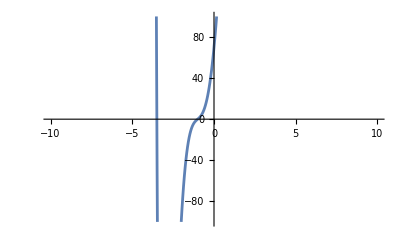

```mathematica
parPI = {τ1->1, δH1->0 ,δP1->1, a->1, δP2 -> 8, ρ->33, k->0.5}
Plot[EqCaraPI/.parPI/.{τ2->0.5, δH2 ->5}, {s,-50,100},
PlotRange->{{-10,10},{-100,100}}]
```

### Focus sur les solutions avec Réel Nul

{τ1→1,δH1→0,δP1→1,a→1,δP2→8,ρ→33,k→100000}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

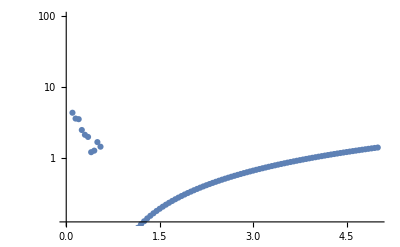

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

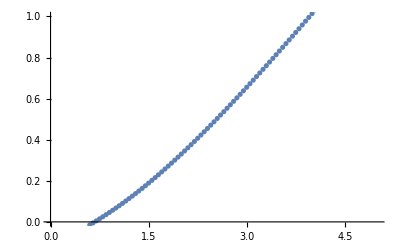

```mathematica
parPI = {τ1->1,δH1->0,δP1->1,a->1,δP2->8,ρ->33,k->100000}
reel=ComplexExpand[Re[EqCaraPI/.{s->x I}/.parPI]];
imag=ComplexExpand[Im[EqCaraPI/.{s->x I}/.parPI]];
xtempo = 2.12;
tP1tempo = 0.5;
VPthierry[tH2_] := tP1/.FindRoot[{reel,imag}/.{δH2->1/tH2, τ2->tP1},{x,xtempo},{tP1,tP1tempo}]
ListPlot[Table[{tH2val, VPthierry[tH2val]}, {tH2val,0.05,5, .05}],
PlotRange->{{0,5},{0,100}},
ScalingFunctions->{None, "Log"}]
ListPlot[Table[{tH2val, VPthierry[tH2val]}, {tH2val,0.05,5, .05}],
PlotRange->{{0,5},{0,1}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

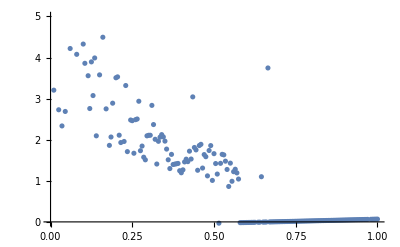

```mathematica
ListPlot[Table[{tH2val, VPthierry[tH2val]}, {tH2val,0.01,1, .005}],
PlotRange->{{0,1},{0,5}}]
```

Ca a l’air bien artéfactuel
Faudrait quand même check le graph type Godfray1989 avec t_ratio,k

## Diagrammes de stabilité tP1-tH2 en fonction de la variab dev. spatiale (k)

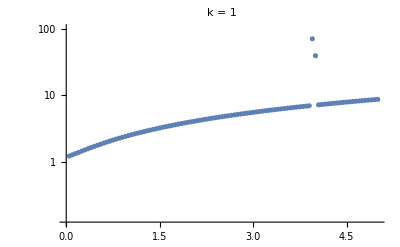

```mathematica
parPI = {τ1->1,δH1->0,δP1->1,a->1,δP2->8,ρ->33,k->1};
reel=ComplexExpand[Re[EqCaraPI/.{s->x I}/.parPI]];
imag=ComplexExpand[Im[EqCaraPI/.{s->x I}/.parPI]];
xtempo = 2.12;
tP1tempo = 0.5;
VPthierry[tH2_] := tP1/.FindRoot[{reel,imag}/.{δH2->1/tH2, τ2->tP1},{x,xtempo},{tP1,tP1tempo}]
ListPlot[Table[{tH2val, VPthierry[tH2val]}, {tH2val,0.05,5, .05}],
PlotRange->{{0,5},{0,100}},
PlotLabel->"k = "<>ToString[k/.parPI],
ScalingFunctions->{None, "Log"}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

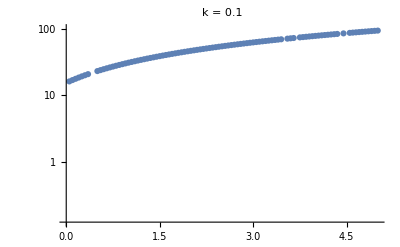

```mathematica
parPI = {τ1->1,δH1->0,δP1->1,a->1,δP2->8,ρ->33,k->0.1};
reel=ComplexExpand[Re[EqCaraPI/.{s->x I}/.parPI]];
imag=ComplexExpand[Im[EqCaraPI/.{s->x I}/.parPI]];
xtempo = 2.12;
tP1tempo = 0.5;
VPthierry[tH2_] := tP1/.FindRoot[{reel,imag}/.{δH2->1/tH2, τ2->tP1},{x,xtempo},{tP1,tP1tempo}]
ListPlot[Table[{tH2val, VPthierry[tH2val]}, {tH2val,0.05,5, .05}],
PlotRange->{{0,5},{0,100}},
PlotLabel->"k = "<>ToString[k/.parPI],
ScalingFunctions->{None, "Log"}]
```

```mathematica
klist=Flatten[{Range[10],{20,50,100, 10000}}];
curvelist={};
ComputeCurvesFunction[kval_]:=Module[{parPI,reel,imag,xtempo=2.12,tP1tempo=0.5},
parPI = {τ1->1,δH1->0,δP1->1,a->1,δP2->8,ρ->33,k->kval};
reel=ComplexExpand[Re[EqCaraPI/. {s->x I}/. parPI]];
imag=ComplexExpand[Im[EqCaraPI/. {s->x I}/. parPI]];
FindtP1Stab[tH2_]:=tP1/. FindRoot[{reel,imag}/. {δH2->1/tH2,τ2->tP1},{x,xtempo},{tP1,tP1tempo}];
Table[{tH2val,FindtP1Stab[tH2val]},{tH2val,0.05,5,0.05}]
];

(*Evaluate for each kval in klist*)
curvelist=ComputeCurvesFunction/@klist;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

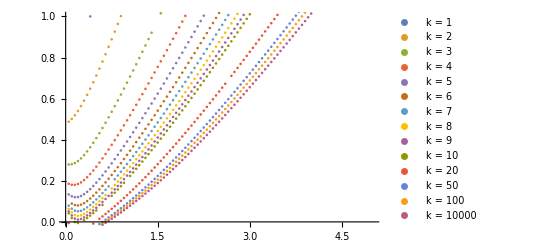

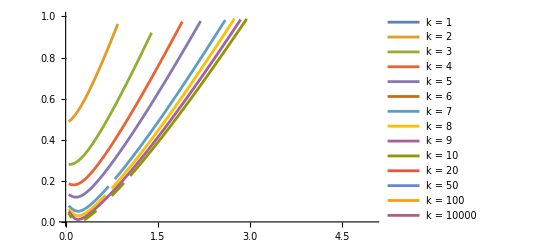

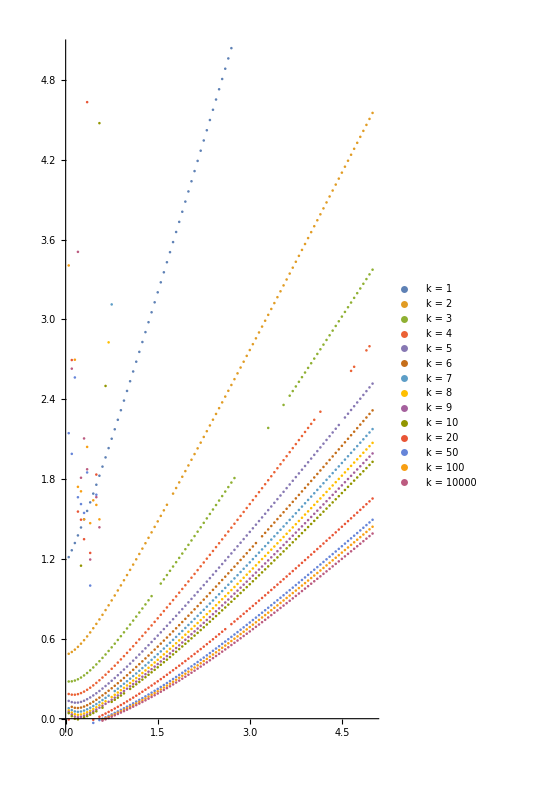

```mathematica
ListPlot[curvelist,
PlotRange->{{0,5},{0,1}},
PlotLegends->StringJoin/@Thread[{"k = ",ToString/@klist}]
]

filteredCurvelist=curvelist/. {x_Real,y_Real}/;!(0<=x<=5&&0<=y<=1):>Missing["Filtered"];
ListLinePlot[filteredCurvelist,
PlotRange->{{0,5},{0,1}},
PlotLegends->StringJoin/@Thread[{"k = ",ToString/@klist}]
]

ListPlot[curvelist,
AspectRatio->2,
ImageSize->{400,800},
PlotRange->{{0,5},{0,5}},
PlotLegends->StringJoin/@Thread[{"k = ",ToString/@klist}]
]
```

## Diagramme de stabilité k-tRatio (type Godfray 1989)

```mathematica
parPIbis = {τ1->1,δH1->0,δP1->1,a->1,δP2->8,ρ->33,δH2-> 1/2.5};
τ2replace = Solve[tRatio == (τ2+1/δP2)/(τ1+1/δH2), τ2][[1]]
```

{τ2→(-δH2+tRatio δP2+tRatio δH2 δP2 τ1)/(δH2 δP2)}

### Technique de résolution avec solution imaginaire pure (?)

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

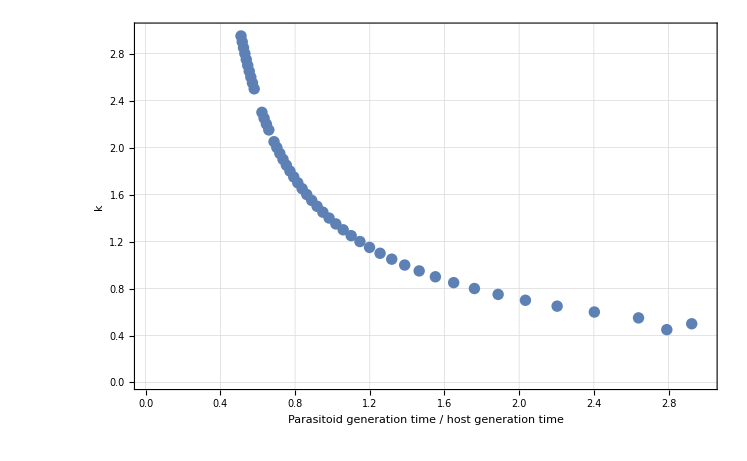

```mathematica
reelbis=ComplexExpand[Re[EqCaraPI/.τ2replace/.{s->x I}/.parPIbis]];
imagbis=ComplexExpand[Im[EqCaraPI/.τ2replace/.{s->x I}/.parPIbis]];
xtempo = 2.12;
tratiotempo = 0.5;
VPthierrybis[kval_] := tRatio/.FindRoot[{reelbis,imagbis}/.{k->kval},{x,xtempo},{tRatio,tratiotempo}]
ListPlot[Table[{VPthierrybis[ki], ki}, {ki,0.05,3, .05}],
PlotRange->{{0,3},{0,3}},
Frame-> True,
GridLines-> Automatic,
ScalingFunctions->{None, None}, 
FrameLabel-> {"Parasitoid generation time / host generation time", "k"}
]
```

### Technique de résolution plus classique

```mathematica
VPbis[tRatioval_, kval_] := s/.FindRoot[EqCaraPI/.τ2replace/.parPIbis/.{tRatio->1tRatioval, k->kval}, {s,1.2}]
VPbis[0,0.1]
VPbis[1,1]
VPbis[1,5]
FindRoot[VPbis[0.3, kroot], {kroot, 0.99}]
```

-0.0291732

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-0.0398382

-1.

FindRoot::nlnum: The function value {-2.2 ((-1.2+0.4 (-1.+Times[«2»])) (-9.2+(2.63647 (1.+Times[«2»]))/Log[«1»]) (-1.2-1. kroot Log[Power[«2»]])+0.13068 kroot Log[33.^(1/kroot)] (-0.146858 33.^Plus[«2»] Power[«2»]^Times[«2»] (1.+Times[«2»]) (-1.+Power[«2»]) kroot-(0.158244 Power[«2»]^Plus[«2»] (1.+Times[«2»]) (-1.2+Times[«2»]) (Times[«2»]+Times[«3»]))/Log[«1»]))} is not a list of numbers with dimensions {1} at {s} = {1.2}.

ReplaceAll::reps: {FindRoot[EqCaraPI/.τ2replace/.parPIbis/.{tRatio→1 0.3,k→kroot},{s,1.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::jsing: Encountered a singular Jacobian at the point {kroot} = {0.99}. Try perturbing the initial point(s).

{kroot→0.99}

Ca correspond pas trop avec la première méthode et aussi trouve rien non plus pour les VP liées aux GCs.

```mathematica
P20temp = 10;
tratiotemp = 0.3;
ktemp = 3;
leqnIC = Flatten[{systemePI, {H1[t/;t<=0] ==10, H2[t/;t<=0] ==10, P1[t/;t<=0] ==10, P2[t/;t<=0] ==10, B[t/;t<=0] ==τ1(k Log[1+a P20temp/k]+ δH1)/.τ2replace/.parPIbis/.{k->ktemp, tRatio->tratiotemp} // N}}];
sol=NDSolve[leqnIC/.τ2replace/.parPIbis/.{k->ktemp, tRatio->tratiotemp}, {H1, H2, P1, P2,B},{t, 0,500}];
```

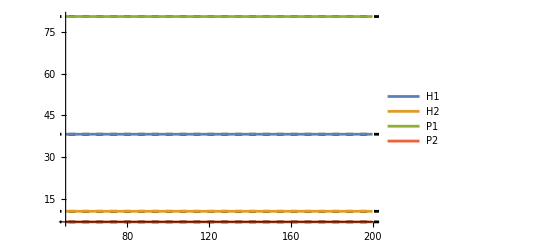

```mathematica
positions={H1eq,H2eq,P1eq,P2eq}/.τ2replace /.parPIbis/.{k->ktemp, tRatio->tratiotemp};
minMax={0,500};
Show[Plot[Evaluate[{H1[t],H2[t], P1[t],P2[t]}/. sol[[1]]],{t,50,200},
PlotLegends->{"H1", "H2", "P1", "P2"},
PlotRange->Full],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{minMax[[1]],x},{minMax[[2]],x}}],{x,positions}]}
]
```

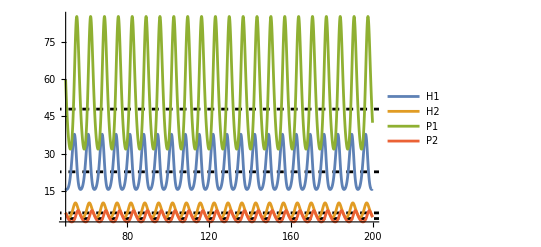

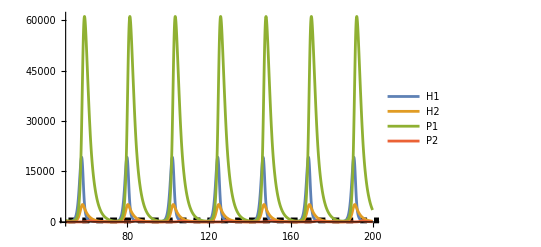

```mathematica
P20temp = 10;
tratiotemp = 0.3;
ktemp = 15;
leqnIC = Flatten[{systemePI, {H1[t/;t<=0] ==10, H2[t/;t<=0] ==10, P1[t/;t<=0] ==10, P2[t/;t<=0] ==10, B[t/;t<=0] ==τ1(k Log[1+a P20temp/k]+ δH1)/.τ2replace/.parPIbis/.{k->ktemp, tRatio->tratiotemp} // N}}];
sol=NDSolve[leqnIC/.τ2replace/.parPIbis/.{k->ktemp, tRatio->tratiotemp}, {H1, H2, P1, P2,B},{t, 0,500}];
positions={H1eq,H2eq,P1eq,P2eq}/.τ2replace /.parPIbis/.{k->ktemp, tRatio->tratiotemp};
minMax={0,500};
Show[Plot[Evaluate[{H1[t],H2[t], P1[t],P2[t]}/. sol[[1]]],{t,50,200},
PlotLegends->{"H1", "H2", "P1", "P2"},
PlotRange->Full],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{minMax[[1]],x},{minMax[[2]],x}}],{x,positions}]}
]

P20temp = 10;
tratiotemp = 1;
ktemp = 15;
leqnIC = Flatten[{systemePI, {H1[t/;t<=0] ==10, H2[t/;t<=0] ==10, P1[t/;t<=0] ==10, P2[t/;t<=0] ==10, B[t/;t<=0] ==τ1(k Log[1+a P20temp/k]+ δH1)/.τ2replace/.parPIbis/.{k->ktemp, tRatio->tratiotemp} // N}}];
sol=NDSolve[leqnIC/.τ2replace/.parPIbis/.{k->ktemp, tRatio->tratiotemp}, {H1, H2, P1, P2,B},{t, 0,500}];
positions={H1eq,H2eq,P1eq,P2eq}/.τ2replace /.parPIbis/.{k->ktemp, tRatio->tratiotemp};
minMax={0,500};
Show[Plot[Evaluate[{H1[t],H2[t], P1[t],P2[t]}/. sol[[1]]],{t,50,200},
PlotLegends->{"H1", "H2", "P1", "P2"},
PlotRange->Full],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{minMax[[1]],x},{minMax[[2]],x}}],{x,positions}]}
]
```

On pourrait dire : “Pas de GCs dans les simulations numériques : les GCs sont non pas créées par l’ajout de PI mais par l’ajout des 2 stades “d’attente””. Mais en réalité, on a des GCs, c’est juste qu’elles sont visibles quand k est très élevé. L’ajout des stades H1,H3 permet de déstabiliser assez le système pour les retrouver à k faible (0.5~1). Pas clair de pq les H1,H3 déstabilisent : si on les considère comme des miniLCT, ils devraient stabiliser (c’est le cas : cf n1,n3 = 300, sensibilité++). Par contre en DDE, ils n’ajoutent aucune variabilité, et alors il y a cet effet d’asynchronisation mis en évidence par Godfray.

## Murdoch 1987 (DDE) : effet de l’ajout de variab dev. (nLCT)

```mathematica
ClearAll;

nn = 10;
mm = 10;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];
ODEkSystem[nn_, mm_]:=Module[{eqns,i},eqns={};
(*Équations pour H[i]*)Do[AppendTo[eqns,D[H[i][t],t]==(-θH-δH1-a P2[t]) H[i][t]+If[i>1,θH H[i-1][t],r H2[t]]],{i,1,nn}];
(*Équation pour H2*)AppendTo[eqns,D[H2[t],t]==θH H[nn][t]-δH2 H2[t]];
(*Équations pour P[i]*)Do[AppendTo[eqns,D[P[i][t],t]==(-θP-δP1) P[i][t]+If[i>1,θP P[i-1][t],a P2[t] H1[t]]],{i,1,mm}];
(*Équation pour P2*)AppendTo[eqns,D[P2[t],t]==θP P[nn][t]-δP2 P2[t]];
eqns];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
system = ODEkSystem[nn, mm];

CreateMatrix[nn_, mm_]:=Module[{J,vars,i},(*Variables du système*)
vars=Join[Table[H[i],{i,1,nn}],{H2},Table[P[i],{i,1,mm}],{P2}];

(*Initialiser la matrice jacobienne avec des zéros*)
J=ConstantArray[0,{nn+mm+2,nn+mm+2}];

(*Remplissage de la sous-matrice pour H[i]*)
Do[J[[i,i]]=-θH-δH1-a P2[t];
If[i>1,J[[i,i-1]]=θH],{i,1,nn}];
(*Remplissage des termes de parasitisme*)
Do[J[[i,nn+mm+2]]=-a*H[i][t],{i,1,nn}];
(*Termes liés à H2*)
J[[1,nn+1]]=r;
(*H1 dépend de H2*)
J[[nn+1,nn]]=θH;
(*H2 dépend de H[k]*)
J[[nn+1,nn+1]]=-δH2;


(*Remplissage de la sous-matrice pour P[i]*)Do[J[[nn+1+i,nn+1+i]]=-θP-δP1;
If[i>1,J[[nn+1+i,nn+i]]=θP],{i,1,mm}];
(*Remplissage des termes de parasitisme*)
Do[J[[nn+2,i]]=a  P2[t],{i,1,nn}];
J[[nn+2, nn+mm+2]] = a*H1[t];
(*Ligne de P2*)
J[[nn+mm+2,nn+mm+1]]=θP;
J[[nn+mm+2,nn+mm+2]]=-δP2;

(*Retourner la matrice jacobienne*)
J];

lJ = CreateMatrix[nn,mm];

fH = θH / (θH + δH1);
fP = θP / (θP + δP1);
P2eqpredi = θH (fH *(r/δH2)^(1/n) - 1)/(a fH) // FullSimplify;
sH = θH / (θH + δH1 + a P2eqpredi);
αH = ∑_(i=0)^(n-1) (sH)^i;
αP = ∑_(i=0)^(m-1) fP^i;
H1eqpredi = δP2/(a*fP^m);
H2eqpredi = H1eqpredi * θH((r/δH2)^(1/n)-1)/(δH2((r/δH2)-1)) // FullSimplify;
P1eqpredi = P2eqpredi * αP * δP2 /(θP*fP^(m-1)) // FullSimplify;

vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
varseq = Flatten[{Table[(H1eqpredi/αH) sH^(i-1),{i,1,nn}],H2eqpredi,Table[(P1eqpredi/αP) fP^(i-1),{i,1,mm}], P2eqpredi}];
lJeq=lJ /.
Thread[vars->varseq];

Clear[r, β];
θH = n*mH;
θP = m*mP;
r = ρ*δH2;


Clear[VP];
params = {mH->1,ρ -> 33,δH1->0,δP2->8, δP1 -> 1, a-> .03}
VP[ta_?NumericQ,t2_?NumericQ]:=Eigenvalues[lJeq/.params/.{n->nn, m->mm,δH2->1/ta, mP->1/t2}][[nn+mm+2]] //N//Re;
```

{mH→1,ρ→33,δH1→0,δP2→8,δP1→1,a→0.03}

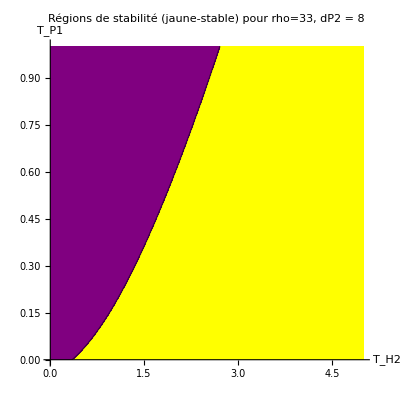

```mathematica
ContourPlot[VP[tH2,tP1],
{tH2,0,5}, {tP1,0,1},
Frame -> False,
Axes -> True,
AxesLabel-> {"T_H2", "T_P1"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
FrameLabel->{"T_H2","T_P1"},
PlotLabel->"Régions de stabilité (jaune-stable) pour rho=33, dP2 = 8"
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

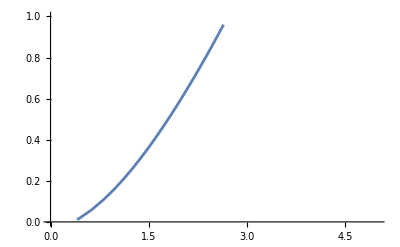

```mathematica
FindtH2rootLCT[tP1val_] := tH2sol/.FindRoot[VP[tH2sol,tP1val], {tH2sol,1.3}]
curvelistLCT = Table[{FindtH2rootLCT[tP1val],tP1val},{tP1val,0.01,1,0.05}];
ListLinePlot[curvelistLCT,
PlotRange->{{0,5},{0,1}},
PlotLegends->"n=m=10"
]
```

## Script qui trouve la limite de stabilité pour une liste de (n,m)

```mathematica
CreateMatrix[nn_, mm_]:=Module[{J,vars,i},(*Variables du système*)
vars=Join[Table[H[i],{i,1,nn}],{H2},Table[P[i],{i,1,mm}],{P2}];

(*Initialiser la matrice jacobienne avec des zéros*)
J=ConstantArray[0,{nn+mm+2,nn+mm+2}];

(*Remplissage de la sous-matrice pour H[i]*)
Do[J[[i,i]]=-θH-δH1-a P2[t];
If[i>1,J[[i,i-1]]=θH],{i,1,nn}];
(*Remplissage des termes de parasitisme*)
Do[J[[i,nn+mm+2]]=-a*H[i][t],{i,1,nn}];
(*Termes liés à H2*)
J[[1,nn+1]]=r;
(*H1 dépend de H2*)
J[[nn+1,nn]]=θH;
(*H2 dépend de H[k]*)
J[[nn+1,nn+1]]=-δH2;


(*Remplissage de la sous-matrice pour P[i]*)Do[J[[nn+1+i,nn+1+i]]=-θP-δP1;
If[i>1,J[[nn+1+i,nn+i]]=θP],{i,1,mm}];
(*Remplissage des termes de parasitisme*)
Do[J[[nn+2,i]]=a  P2[t],{i,1,nn}];
J[[nn+2, nn+mm+2]] = a*H1[t];
(*Ligne de P2*)
J[[nn+mm+2,nn+mm+1]]=θP;
J[[nn+mm+2,nn+mm+2]]=-δP2;

(*Retourner la matrice jacobienne*)
J];

mH1par = 1;
δH1par = 0;

δP1par = 0.1;
δP2par = 8;

ρpar = 33;
apar = 1;
paramsplot = {mH->mH1par, δH1->δH1par, δP1->δP1par, δP2->δP2par, ρ->ρpar, a-> apar,δH2 -> 1/tH2, mP -> 1/tP1 }

nmValues=Join[Range[1,20], {30,40,50,100}];

(*Storage for results*)
StabilityCurveData={};

(*Loop through parameter values*)
Monitor[
For[
i=1,i<=Length[nmValues],i++,Module[{currentN=nmValues[[i]],sol,analysis},(*Set up the system with current n=m value*)
nn=currentN;
mm=currentN;
Clear[δP1,n,m, δH1, δP1, δH2, δP2, ρ,β, mP, mH]; 

H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];

fH = θH / (θH + δH1);
fP = θP / (θP + δP1);
P2eqpredi = θH (fH *(r/δH2)^(1/n) - 1)/(a fH) // FullSimplify;
sH = θH / (θH + δH1 + a P2eqpredi);
αH = ∑_(i=0)^(n-1) (sH)^i;
αP = ∑_(i=0)^(m-1) fP^i;
H1eqpredi = δP2/(a*fP^m);
H2eqpredi = H1eqpredi * θH((r/δH2)^(1/n)-1)/(δH2((r/δH2)-1)) // FullSimplify;
P1eqpredi = P2eqpredi * αP * δP2 /(θP*fP^(m-1)) // FullSimplify;

θH = n*mH;
θP = m*mP;
r = ρ*δH2;
Clear[δH1]; (* On utilise les mortalités intrinsèques telles quelles*)
Clear[δP1];

lJ = CreateMatrix[nn,mm];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
varseq = Flatten[{Table[(H1eqpredi/αH) sH^(i-1),{i,1,nn}],H2eqpredi,Table[(P1eqpredi/αP) fP^(i-1),{i,1,mm}], P2eqpredi}];
lJeq=lJ /.
Thread[vars->varseq];

	
Clear[VP];
VP[X_?NumericQ,Y_?NumericQ]:=Module[
{eigs},
eigs=lJeq/.paramsplot/.{n->nn, m->mm}/.{tH2->X, tP1->Y} //N// Eigenvalues;
If[Length[eigs]>=nn+mm+2,eigs[[nn+mm+2]] // Re,Indeterminate (*Return a safe fallback*)]
];

τ2Min=0.01;
τ2Max=1;
τ2Pas=0.02;
	
CourbeLimite={};

For[t2=τ2Max,t2>τ2Min,t2-=τ2Pas,
Module[{tsol},
(*Print["t2 = ",t2];*)
tsol=Check[ta/. FindRoot[VP[ta,t2],{ta,0.01,5},Method->"Brent"],"Failed"]; (*Use Quiet to suppress warnings,Check to handle failures*)
If[NumericQ[tsol]&&tsol>0,
AppendTo[CourbeLimite,{tsol,t2}]
(*Print["Skipping t2 = ",t2," (FindRoot failed)"]*)]
]
];

AppendTo[StabilityCurveData, CourbeLimite]
]
],{i,Length[nmValues]}
]
```

{mH→1,δH1→0,δP1→0.1,δP2→8,ρ→33,a→1,δH2→1/tH2,mP→1/tP1}

## Comparaison des deux formes d’agrégation des risques

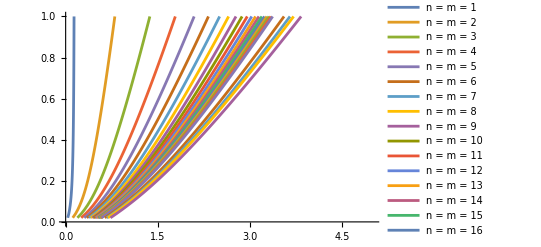

-Graphics-

```mathematica
ListLinePlot[StabilityCurveData,
PlotRange->{{0,5},{0,1}},
PlotLegends->StringJoin/@Thread[{"n = m = ",ToString/@nmValues}]
]

ListLinePlot[filteredCurvelist,
PlotRange->{{0,5},{0,1}},
PlotLegends->StringJoin/@Thread[{"k = ",ToString/@klist}]
]
```

## Comportement quand tH2 -> 0

## Fixed delay and pseudointerference

```mathematica
Limit[EqCaraPI, δH2->+ ∞] // FullSimplify
```

1/(Sign[s] Sign[Log[ⅇ^(-δH1/k) ρ^(1/(k τ1))]])ⅇ^(2 (s+δH1) τ1+(s+δP1) τ2-ⅈ Im[3 (s+δH1) τ1+(2 s+δP1) τ2+k τ1 Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]]) (s+δP1) ρ^(-1/(k τ1)) (-∞) (-s (s+δH1) δP2 (ⅇ^(δH1/k)-ρ^(1/(k τ1))) (-ρ+ⅇ^((s+δH1) τ1) (ⅇ^(-δH1/k) ρ^(1/(k τ1)))^(k τ1))+Log[ⅇ^(-δH1/k) ρ^(1/(k τ1))] (ⅇ^(δH1/k) (-1+ⅇ^(s τ1)) k δP2 ρ (δH1+k Log[ⅇ^(-δH1/k) ρ^(1/(k τ1))])+ρ^(1/(k τ1)) (-ⅇ^(δH1 τ1+s (τ1+τ2)) s (s+δP2) (ⅇ^(-δH1/k) ρ^(1/(k τ1)))^(k τ1) (s+δH1+k Log[ⅇ^(-δH1/k) ρ^(1/(k τ1))])+ρ (-((-1+ⅇ^(s τ1)) k δH1 δP2)+ⅇ^(s τ2) s (s+δH1) (s+δP2)+k (k δP2-ⅇ^(s τ1) k δP2+ⅇ^(s τ2) s (s+δP2)) Log[ⅇ^(-δH1/k) ρ^(1/(k τ1))]))))

```mathematica
EqCaraPI /. δH2 -> 1/tH2
```

(-s-δP1) (ⅇ^(-((s+δP1) τ2)) k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))] (-(ⅇ^(-((s+δH1) τ1)+δP1 τ2) (ⅇ^((-δH1 τ1+Log[ρ])/(k τ1)))^(-k τ1) (-1+ⅇ^(s τ1)) (1-ⅇ^(-τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))) δP2 ρ^(2-1/(k τ1)) (-ⅇ^(δH1/k)+ρ^(1/(k τ1))) (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))/(s tH2 (-1+ρ) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])-(ⅇ^(-δH1/k-(s+δH1) τ1+δP1 τ2) δP2 (ⅇ^(-δH1/k) ρ^(1/(k τ1)))^(-1-k τ1) (ⅇ^(δH1/k)-ρ^(1/(k τ1))) (-s+(-1+ⅇ^(-τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])) ρ)/tH2) (ⅇ^(τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])) s (-1+ρ)-(-1+ⅇ^(s τ1)) ρ (δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])))/(s (-1+ρ) Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]))+(-s+(-1+ⅇ^(-τ1 (s+δH1+k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))])) ρ)/tH2) (-s-δH1-k Log[ⅇ^((-δH1 τ1+Log[ρ])/(k τ1))]) (-s-δP2+(ⅇ^(-s τ2) δP2 (1-ⅇ^(δH1/k) ρ^(-1/(k τ1))))/Log[ⅇ^(-δH1/k) ρ^(1/(k τ1))]))

Linéariser MH1(t) : 
MH1(t) = ρ δH2 (H2* + h2(t-T1)) exp(-∫_(t-T1)^t (k ln[1+a/k(P2* + p2(u))]+δH1)ⅆu)
-> Murdoch 1987 : mh1(t) = δH2 h2(t-T1) - a δH2 H2* ∫_(t-T1)^t p2(u)ⅆu  + I(...)
-> Quentin : mh1(t) = ρ δH2 exp(-T1(aP2* + δH1)) [h2(t-T1) - H2*∫_(t-T1)^t (a p2(u)+δH1)ⅆu]
-> Mathis pour k-> ∞ : mh1(t) = ρ δH2 exp(-T1(aP2*+δH1))[h2(t-T1) - H2*∫_(t-T1)^t a p2(u)ⅆu]